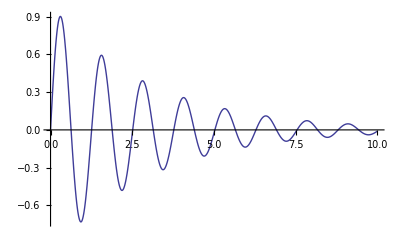

3 ⅈ √(π/2) DiracDelta[(-15+ⅈ)+3 ω]-3 ⅈ √(π/2) DiracDelta[(15+ⅈ)+3 ω]

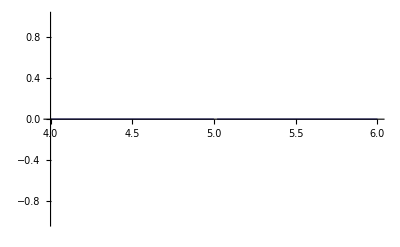

```mathematica
S[x_,k_,τ_]:=Sin[k x]Exp[-x/τ]
Plot[S[x,5,3],{x,0,10}]
FourierTransform[S[x,5,3],x,ω]
Plot[Abs[FourierTransform[S[x,5,3],x,ω]],{ω,4,6}]
```